```mathematica
(*Define the ftilde  function*)
```

```mathematica
f[x_,y_,sigma_]:=Erf[Abs[x-y]/(2*sigma)]/Abs[x-y]
```

```mathematica
f[x_,x_,sigma_]:=1/(sigma*Sqrt[Pi])
```

```mathematica
(*define the function for particle indices: if they are different, add a transversal distance d*)
fPart[j_,k_,x_,y_,sigma_,d_]:=If[j==k,f[x,y,sigma],Erf[Sqrt[d^2+(x-y)^2]/(2*sigma)]/Sqrt[d^2+(x-y)^2]]
```

```mathematica
(*expression for g(x,y), assuming two particles of masses m[[0]], m[[1]]*)
g[x_,y_, m_, sigma_,d_]:=Sum[m[[j]]*m[[k]]*((I-1)*fPart[j,k,x[[j]],x[[k]],sigma,d]+(-I-1)*fPart[j,k,y[[j]],y[[k]], sigma,d]+2*fPart[j,k,x[[j]],y[[k]],sigma,d]),{j,1,2},{k,1,2}]
```

```mathematica
(*module to create a two-dimensional vector in the computational basis*)
```

```mathematica
Vect2[l_]:=Module[{v},
v=ConstantArray[0,{2,1}];
v[[l]]={1};
v]
```

```mathematica
(*code to generate the qubit projectors |l><l|*)
```

```mathematica
Proj2[l_]:=Module[{P},
P=ConstantArray[0,{2,2}];
P[[l]][[l]]=1;
P]
```

```mathematica
(*Code to generate A in superoperator form, i.e. A=\sum_{x,y}g(x,y)|x><x|\otimes |y><y|. The two position values for the first (second) particle are encoded in the entries of s (t) *)
```

```mathematica
Lindblad[s_,t_, m_,sigma_,d_]:=Module[{},
Sum[KroneckerProduct[Proj2[j1],Proj2[j2],Proj2[k1],Proj2[k2]]*g[{s[[j1]],t[[j2]]},{s[[k1]],t[[k2]]}, {m[[1]],m[[2]]}, sigma,d],{j1,1,2},{j2,1,2},{k1,1,2},{k2,1,2}]
]
```

```mathematica
(*define A (in superoperator form). Note that the y coordinates of both particles are 0 and L: they are only distinguished by the x coordinate, which separates them by a distance d*)
```

```mathematica
A=Lindblad[{0,L},{0,L},{m,m},sigma,d];
```

```mathematica
(*states: pure and mixed*)
```

```mathematica
(*|+>^{\otimes 2}*)
```

```mathematica
vPlus={{1},{1},{1},{1}}/2;
```

```mathematica
(*|->^{\otimes 2}*)
```

```mathematica
vMinus={{1},{-1},{-1},{1}}/2;
```

```mathematica
(*\rho_0=|+><+|^{\otimes 2}: *)
rho0=vPlus.Transpose[vPlus];
```

```mathematica
(*A acting on \rho_0*)
```

```mathematica
Arho0=ArrayReshape[A.ArrayReshape[rho0,{16,1}],{4,4}];
```

```mathematica
(*partial transposition of a two-qubit state*)
PartialTranspose[rho_]:=Sum[KroneckerProduct[IdentityMatrix[2],Vect2[j].Transpose[Vect2[k]]].rho.KroneckerProduct[IdentityMatrix[2],Vect2[j].Transpose[Vect2[k]]],{k,1,2},{j,1,2}]
```

```mathematica
(*compute the matrix (1-|+><+|^{\otimes 2})A(rho_0)^{T_1}(1-|+><+|^{\otimes 2})*)
```

```mathematica
specialMatrix=(IdentityMatrix[4]-rho0).PartialTranspose[Arho0].(IdentityMatrix[4]-rho0);
```

```mathematica
eige=Simplify[Eigenvalues[specialMatrix],Assumptions->{d>0, sigma>0}]
```

{0,0,m^2 (1/(√π sigma)-(√2 √((d^2+L^2) Erf[d/(2 sigma)]^2-2 d √(d^2+L^2) Erf[d/(2 sigma)] Erf[(√(d^2+L^2))/(2 sigma)]+d^2 Erf[(√(d^2+L^2))/(2 sigma)]^2))/(d √(d^2+L^2))-Erf[Abs[L]/(2 sigma)]/Abs[L]),m^2 (1/(√π sigma)+(√2 √((d^2+L^2) Erf[d/(2 sigma)]^2-2 d √(d^2+L^2) Erf[d/(2 sigma)] Erf[(√(d^2+L^2))/(2 sigma)]+d^2 Erf[(√(d^2+L^2))/(2 sigma)]^2))/(d √(d^2+L^2))-Erf[Abs[L]/(2 sigma)]/Abs[L])}

```mathematica
(*The expressions for the two non-zero eigenvalues coincide with those provided in the paper*)
```

```mathematica
(*We next verify that one of the zero eigenvalues of the matrix has eigenvector |- >^{\otimes 2}*)
```

```mathematica
Simplify[specialMatrix.vMinus]
```

{{0},{0},{0},{0}}

```mathematica
(*second order pertubration theory*)
(*First, compute the matrix element <phi_0|A(rho_0)^{T_1}|phi_3>*)
```

```mathematica
overlapPlusMin=Simplify[Transpose[vPlus].PartialTranspose[Arho0].vMinus][[1,1]]
```

m^2 (Erf[(√(d^2))/(2 sigma)]/(√(d^2))-Erf[(√(d^2+L^2))/(2 sigma)]/(√(d^2+L^2)))

```mathematica
(*overlap <phi_3|\ddot{rho}(0)|phi_3>*)
```

```mathematica
A2rho0=ArrayReshape[A.A.ArrayReshape[rho0,{16,1}],{4,4}];
```

```mathematica
overlapMinMin=Simplify[Transpose[vMinus].PartialTranspose[A2rho0].vMinus][[1,1]]
```

2 m^4 ((3 Erf[(√(d^2))/(2 sigma)]^2)/d^2-(6 Erf[(√(d^2))/(2 sigma)] Erf[(√(d^2+L^2))/(2 sigma)])/(√(d^2) √(d^2+L^2))+(d^2+L^2+3 π sigma^2 Erf[(√(d^2+L^2))/(2 sigma)]^2)/((d^2+L^2) π sigma^2)-(2 Erf[Abs[L]/(2 sigma)])/(√π sigma Abs[L])+Erf[Abs[L]/(2 sigma)]^2/Abs[L]^2)

```mathematica
(*second order eigenvalue for |\phi_3> (remember that we are omiting the pre-factor (G/2\hbar)^2*)
```

```mathematica
lambda3=Simplify[overlapMinMin-2*overlapPlusMin^2, Assumptions->{d>0}]
```

2 m^4 ((2 Erf[d/(2 sigma)]^2)/d^2-(4 Erf[d/(2 sigma)] Erf[(√(d^2+L^2))/(2 sigma)])/(d √(d^2+L^2))+(d^2+L^2+2 π sigma^2 Erf[(√(d^2+L^2))/(2 sigma)]^2)/((d^2+L^2) π sigma^2)-(2 Erf[Abs[L]/(2 sigma)])/(√π sigma Abs[L])+Erf[Abs[L]/(2 sigma)]^2/Abs[L]^2)

```mathematica
(*verify if this complicated expression ca be written more succintly*)
```

```mathematica
lambda3Simple=2*m^4*((1/(Sqrt[Pi]*sigma)-f[L,0,sigma])^2+2*(f[d,0,sigma]-f[Sqrt[d^2+L^2],0,sigma])^2)
```

2 m^4 ((1/(√π sigma)-Erf[Abs[L]/(2 sigma)]/Abs[L])^2+2 (Erf[Abs[d]/(2 sigma)]/Abs[d]-Erf[(√Abs[d^2+L^2])/(2 sigma)]/(√Abs[d^2+L^2]))^2)

```mathematica
Simplify[lambda3-lambda3Simple,Assumptions->{d>0,L>0}]
```

0

```mathematica
(*explore for which values of L EMinus is negative for greater distances d (since the value of sigma just rescales the graph, we take sigma=1)*)
```

```mathematica
expr=eige[[3]]/.{sigma->1}
```

m^2 (1/(√π)-(√2 √((d^2+L^2) Erf[d/2]^2-2 d √(d^2+L^2) Erf[d/2] Erf[1/2 √(d^2+L^2)]+d^2 Erf[1/2 √(d^2+L^2)]^2))/(d √(d^2+L^2))-Erf[Abs[L]/2]/Abs[L])

```mathematica
maxDist[L_]:=FindRoot[(1/(√π)-(√2 √((d^2+L^2) Erf[d/2]^2-2 d √(d^2+L^2) Erf[d/2] Erf[1/2 √(d^2+L^2)]+d^2 Erf[1/2 √(d^2+L^2)]^2))/(d √(d^2+L^2))-Erf[Abs[L]/2]/Abs[L]),{d,1}][[1,2]]
```

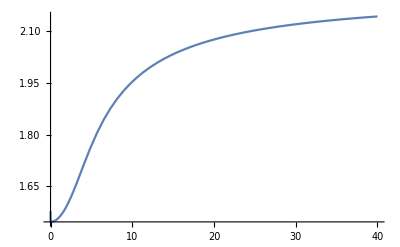

```mathematica
Plot[maxDist[L],{L,0.001,40}]
```

```mathematica
(*High values of L allow a greater positive distance d between the two particles*)
```

```mathematica
(*find maximum distance*)
```

```mathematica
FindRoot[1/Sqrt[Pi]-Sqrt[2]*f[d,0,1],{d,1}]
```

{d→2.21093}

```mathematica
(*The maximum distance that allows GIE in this configuration is 2.21093\sigma*)
```